# Circumcircle

### Author

Eric W. Weisstein
August 10, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneGeometry/Circumcircle.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Circumcircle.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Diagram

#### V5

```mathematica
CircumcircleDiagram[v_List]:=Module[{},
tri=Triangle[v];
vert[i_]:=Vertices[tri][[i]];
foot[i_]:=Foot[PerpendicularBisectors[tri][[i]]];
pts={
TarryPoint,"T",SteinerPoint,"S",
Circumcenter,"O",
vert[1],"A",vert[2],"B",vert[3],"C"
};
redpts={foot[1],"M_A",foot[2],"M_B",foot[3],"M_C"};

{
ClosedLine[v],
EqualSideTicksAboutMidpoints[tri,.05],
Circumcircle[tri],
{
Red,
PerpendicularBisectors[tri],
PointLabels[tri,redpts,.03],
PerpSquare[{#,PerpendicularLine[Circumcenter[tri],#]},.08,3]&/@Sides[tri]
},
{Green,Line[Coordinates/@{TarryPoint[tri],SteinerPoint[tri]}]},
{Blue,Line[{Coordinates@Circumcenter[tri],#}]&/@Vertices[tri]},
PointLabels[tri,pts,.03]
}
]
```

```mathematica
Show[Graphics[CircumcircleDiagram[{{0.,-.5},{1.3,1.7},{3.,-.4}}]],AspectRatio->Automatic]
```

⁃Graphics⁃

#### V6

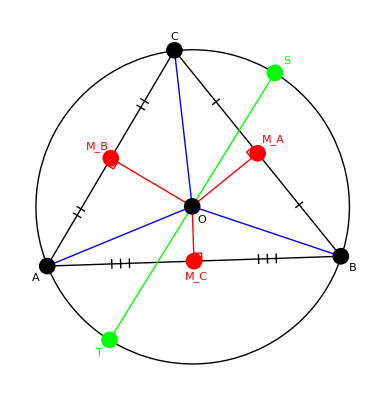

```mathematica
CircumcircleDiagram[v_List]:=Module[{tri=Triangle[v]},
{
ClosedLine[v],
EqualSideTicksAboutMidpoints[tri,.05],
Circumcircle[tri],
{
Red,
PerpendicularBisectors[tri],
PointLabels[Transpose[{
Subscript["M",#]&/@{"A","B","C"},
#[[1,2]]&/@PerpendicularBisectors[tri],
{LabelOffset->{.16,.14},LabelOffset->{-.14,.12},LabelOffset->{.02,-.16}}
}]],
PerpSquare[{#,PerpendicularLine[Circumcenter[tri],#]},.08,2]&/@Sides[tri]
},
{Green,
Line[Coordinates/@{TarryPoint[tri],SteinerPoint[tri]}],
PointLabels[{{"T",TarryPoint[tri][[1]],LabelOffset->{-.1,-.13}},{"S",SteinerPoint[tri][[1]],LabelOffset->.12}}]
},
{Blue,Line[{Coordinates@Circumcenter[tri],#}]&/@Vertices[tri]},
PointLabels[Transpose[{{"A","B","C","O"},Append[Vertices[tri],Circumcenter[tri][[1]]],{LabelOffset->-.12,LabelOffset->{.12,-.12},LabelOffset->{0,.14},LabelOffset->{.1,-.14}}}]]
(*
MyPointLabels/@{
{Circumcenter[tri],"O"},
Sequence@@Transpose[{VertexPoints[tri],{"A","B","C"}}]
}
*)
}
]
Graphics[CircumcircleDiagram[{{0.,-.5},{3.,-.4},{1.3,1.7}}]]
```

## Three-Point Cartesian

```mathematica
(m=Join[{{x^2+y^2,x,y,1}},
Table[{x[i]^2+y[i]^2,x[i],y[i],1},{i,3}]
])/.a_[n_]:>Subscript[a,n]//MatrixForm//TraditionalForm
```

(x^2+y^2 | x | y | 1
x_1^2+y_1^2 | x_1 | y_1 | 1
x_2^2+y_2^2 | x_2 | y_2 | 1
x_3^2+y_3^2 | x_3 | y_3 | 1)

```mathematica
ma=Transpose[Rest[Transpose[Rest[m]]]];
```

```mathematica
MatrixForm[ma]
```

(x[1] | y[1] | 1
x[2] | y[2] | 1
x[3] | y[3] | 1)

```mathematica
Equal@@Prepend[Det[ma],Coefficient[Expand[Det[m]],#^2]&/@{x,y}]
```

True

```mathematica
mb=Coefficient[Expand[Det[m]],#]&/@{x ,y};
```

```mathematica
mb2=Table[Transpose[Drop[Transpose[Rest[m]],{i+1}]],{i,2}];
```

```mathematica
MatrixForm/@mb2
```

{(x[1]^2+y[1]^2 | y[1] | 1
x[2]^2+y[2]^2 | y[2] | 1
x[3]^2+y[3]^2 | y[3] | 1),(x[1]^2+y[1]^2 | x[1] | 1
x[2]^2+y[2]^2 | x[2] | 1
x[3]^2+y[3]^2 | x[3] | 1)}

```mathematica
mb[[1]]+Det[mb2[[1]]]
```

0

```mathematica
mb[[2]]-Det[mb2[[2]]]
```

0

```mathematica
mc=-Transpose[Drop[Transpose[Rest[m]],-1]];
```

```mathematica
mc//MatrixForm
```

(-x[1]^2-y[1]^2 | -x[1] | -y[1]
-x[2]^2-y[2]^2 | -x[2] | -y[2]
-x[3]^2-y[3]^2 | -x[3] | -y[3])

```mathematica
SameQ@@{Det[mc],CoefficientList[Expand[Det[m]],{x,y}][[1,1]]}
```

True

```mathematica
Expand[Det[m]-(Det[ma](x^2+y^2)+mb[[1]] x+mb[[2]]y+Det[mc])]
```

0

### Check

```mathematica
CircumcircleMatrix[l_List,{xx_,yy_}]:=Module[{i},
Join[{{xx^2+yy^2,xx,yy,1}},Table[{x[i]^2+y[i]^2,x[i],y[i],1},{i,3}]]/.Flatten[Table[Thread[{x[i],y[i]}->l[[i]]],{i,3}]]
]
```

```mathematica
CircumcircleConstants[l_List]:=Module[
{
m=Rest[CircumcircleMatrix[l,{xx,yy}]],
i
},
{
Det[Transpose[Rest[Transpose[m]]]],
Table[(-1)^(i+1) Det[Transpose[Drop[Transpose[m],{i+1}]]],{i,2}],
Det[Transpose[Drop[Transpose[m],-1]]]
}
]
```

```mathematica
pts={{0,0},{1,0},{4,6}};
```

```mathematica
{aa,bb,cc}=CircumcircleConstants[pts]
```

{6,{6,48},0}

```mathematica
{Circle[bb/(2aa),Sqrt[bb.bb-4aa cc]/(2aa)],
Circumcircle[pts]}
```

{Circle[{1/2,4},(√65)/2],Circle[{1/2,4},(√65)/2]}

```mathematica
And@@Table[pts=Table[Random[Real,{-5,5}],{3},{2}];
{aa,bb,cc}=CircumcircleConstants[pts];
Circle[bb/(2aa),Sqrt[bb.bb+4aa cc]/(2Abs[aa])]==
Circumcircle[pts],
{100}]
```

True

## Equation

```mathematica
CircleFunction[Circumcircle]
```

0

```mathematica
CircleEquation[Circumcircle]
```

c α β+b α γ+a β γ

```mathematica
FullSimplify[DistanceTrilinears[CircleEquation[Circumcenter,Circumradius[]]],TriangleQ[]]
```

-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (c α β+b α γ+a β γ))/(4 a b c)

## Center

```mathematica
CircleCenter[Circumcircle]
```

{Cos[A],Cos[B],Cos[C]}

```mathematica
Trilinears[Circumcenter]
```

{Cos[A],Cos[B],Cos[C]}

```mathematica
IncidentCenters[KimberlingCenters,α-Cos[A]]
```

{X[3]}

```mathematica
CenterName/@%
```

{circumcenter}

### Circle Function

```mathematica
IncidentCenters[KimberlingCenters,CyclicTrilinears[CircleFunction[Circumcircle]]]
```

{}

```mathematica
CircleFunction[Circumcircle]
```

0

## Radius

```mathematica
Together//@DistanceTrilinears[CircleRadius[Circumcircle]]
```

(√(a^2 b^2 c^2))/(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))

```mathematica
Simplify[%,a>0&&b>0&&c>0]
```

(a b c)/(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))

```mathematica
Circumradius[]
```

(a b c)/(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))

## Incident Centers

Rehashing triangle centers...

```mathematica
(ctrs=IncidentCenters[KimberlingCenters,Circumcircle])//Timing
```

{20.7288 Second,{X[74],X[98],X[99],X[100],X[101],X[102],X[103],X[104],X[105],X[106],X[107],X[108],X[109],X[110],X[111],X[112],X[476],X[477],X[675],X[681],X[689],X[691],X[697],X[699],X[701],X[703],X[705],X[707],X[709],X[711],X[713],X[715],X[717],X[719],X[721],X[723],X[725],X[727],X[729],X[731],X[733],X[735],X[737],X[739],X[741],X[743],X[745],X[747],X[753],X[755],X[759],X[761],X[767],X[769],X[773],X[777],X[779],X[781],X[783],X[785],X[787],X[789],X[791],X[793],X[795],X[797],X[803],X[805],X[807],X[809],X[813],X[815],X[817],X[819],X[825],X[827],X[831],X[833],X[835],X[839],X[840],X[841],X[842],X[843],X[898],X[901],X[907],X[915],X[917],X[919],X[925],X[927],X[929],X[930],X[931],X[932],X[933],X[934],X[935],X[953],X[972],X[1113],X[1114],X[1141],X[1286],X[1287],X[1288],X[1289],X[1290],X[1291],X[1292],X[1293],X[1294],X[1295],X[1296],X[1297],X[1298],X[1299],X[1300],X[1301],X[1302],X[1303],X[1304],X[1305],X[1306],X[1307],X[1308],X[1309],X[1310],X[1311],X[1379],X[1380],X[1381],X[1382],X[1477],X[2222],X[2249],X[2291],X[2365],X[2366],X[2367],X[2368],X[2369],X[2370],X[2371],X[2372],X[2373],X[2374],X[2375],X[2376],X[2377],X[2378],X[2379],X[2380],X[2381],X[2382],X[2383],X[2384],X[2687],X[2688],X[2689],X[2690],X[2691],X[2692],X[2693],X[2694],X[2695],X[2696],X[2697],X[2698],X[2699],X[2700],X[2701],X[2702],X[2703],X[2704],X[2705],X[2706],X[2707],X[2708],X[2709],X[2710],X[2711],X[2712],X[2713],X[2714],X[2715],X[2716],X[2717],X[2718],X[2719],X[2720],X[2721],X[2722],X[2723],X[2724],X[2725],X[2726],X[2727],X[2728],X[2729],X[2730],X[2731],X[2732],X[2733],X[2734],X[2735],X[2736],X[2737],X[2738],X[2739],X[2740],X[2741],X[2742],X[2743],X[2744],X[2745],X[2746],X[2747],X[2748],X[2749],X[2750],X[2751],X[2752],X[2753],X[2754],X[2755],X[2756],X[2757],X[2758],X[2759],X[2760],X[2761],X[2762],X[2763],X[2764],X[2765],X[2766],X[2767],X[2768],X[2769],X[2770],X[2855],X[2856],X[2857],X[2858],X[2859],X[2860],X[2861],X[2862],X[2863],X[2864],X[2865],X[2866],X[2867],X[2868]}}

```mathematica
First/@ctrs
```

{74,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,476,477,675,681,689,691,697,699,701,703,705,707,709,711,713,715,717,719,721,723,725,727,729,731,733,735,737,739,741,743,745,747,753,755,759,761,767,769,773,777,779,781,783,785,787,789,791,793,795,797,803,805,807,809,813,815,817,819,825,827,831,833,835,839,840,841,842,843,898,901,907,915,917,919,925,927,929,930,931,932,933,934,935,953,972,1113,1114,1141,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1379,1380,1381,1382,1477,2222,2249,2291,2365,2366,2367,2368,2369,2370,2371,2372,2373,2374,2375,2376,2377,2378,2379,2380,2381,2382,2383,2384,2687,2688,2689,2690,2691,2692,2693,2694,2695,2696,2697,2698,2699,2700,2701,2702,2703,2704,2705,2706,2707,2708,2709,2710,2711,2712,2713,2714,2715,2716,2717,2718,2719,2720,2721,2722,2723,2724,2725,2726,2727,2728,2729,2730,2731,2732,2733,2734,2735,2736,2737,2738,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2770,2855,2856,2857,2858,2859,2860,2861,2862,2863,2864,2865,2866,2867,2868}

```mathematica
Length[ctrs]
```

256

```mathematica
{#,CenterName[#]}&/@ctrs//TableForm
```

X[74] | X(74)
X[98] | Tarry point
X[99] | Steiner point
X[100] | anticomplement of Feuerbach point
X[101] | &psi;(incenter, symmedian point)
X[102] | &lambda;(incenter, orthocenter)
X[103] | antipode of X(101)
X[104] | antipode of X(100)
X[105] | &lambda;(incenter, symmedian point)
X[106] | &lambda;(incenter, centroid)
X[107] | &psi;(symmedian point, orthocenter)
X[108] | &psi;(circumcenter, orthocenter)
X[109] | &psi;(incenter, circumcenter)
X[110] | focus of Kiepert parabola
X[111] | Parry point
X[112] | &psi;(orthocenter, symmedian point)
X[476] | Tixier point
X[477] | Tixier antipode
X[675] | trilinear pole of line X(6)X(514)
X[681] | trilinear pole of line X(6)X(158)
X[689] | trilinear pole of line X(6)X(76)
X[691] | trilinear pole of line X(6)X(110)
X[697] | even (- 4, - 3) circumcircle point
X[699] | even (- 4, - 2) circumcircle point
X[701] | even (- 4, - 1) circumcircle point
X[703] | even (- 4, 0) circumcircle point
X[705] | even (- 4, 1) circumcircle point
X[707] | even (- 4, 2) circumcircle point
X[709] | even (- 4, 3) circumcircle point
X[711] | even (- 4, 4) circumcircle point
X[713] | even (- 3, - 2) circumcircle point
X[715] | even (- 3, - 1) circumcircle point
X[717] | even (- 3, 0) circumcircle point
X[719] | even (- 3, 1) circumcircle point
X[721] | even (- 3, 0) circumcircle point
X[723] | even (- 3, 3) circumcircle point
X[725] | even (- 3, 4) circumcircle point
X[727] | even (- 2, -1) circumcircle point
X[729] | even (- 2, 0) circumcircle point
X[731] | even (- 2, 1) circumcircle point
X[733] | even (- 2, 2) circumcircle point
X[735] | even (- 2, 3) circumcircle point
X[737] | even (- 2, 4) circumcircle point
X[739] | even (- 1, 0) circumcircle point
X[741] | even (- 1, 1) circumcircle point
X[743] | even (- 1, 2) circumcircle point
X[745] | even (- 1, 3) circumcircle point
X[747] | even (- 1, 4) circumcircle point
X[753] | even (0, 3) circumcircle point
X[755] | even (0, 4) circumcircle point
X[759] | even (1, 3) circumcircle point
X[761] | even (1, 4) circumcircle point
X[767] | even (3, 4) circumcircle point
X[769] | o-(- 4, - 3) circumcircle point
X[773] | o-(- 4, - 1) circumcircle point
X[777] | o-(- 4, 1) circumcircle point
X[779] | o-(- 4, 2) circumcircle point
X[781] | o-(- 4, 3) circumcircle point
X[783] | o-(- 4, 4) circumcircle point
X[785] | o-(- 3, - 2) circumcircle point
X[787] | o-(- 3, - 1) circumcircle point
X[789] | o-(- 3, 0) circumcircle point
X[791] | o-(- 3, 1) circumcircle point
X[793] | o-(- 3, 2) circumcircle point
X[795] | o-(- 3, 3) circumcircle point
X[797] | o-(- 3, 4) circumcircle point
X[803] | o-(- 2, 1) circumcircle point
X[805] | o-(- 2, 2) circumcircle point
X[807] | o-(- 2, 3) circumcircle point
X[809] | o-(- 2, 4) circumcircle point
X[813] | o-(- 1, 1) circumcircle point
X[815] | o-(- 1, 2) circumcircle point
X[817] | o-(- 1, 3) circumcircle point
X[819] | o-(- 1, 4) circumcircle point
X[825] | o-(0, 3) circumcircle point
X[827] | o-(0, 4) circumcircle point
X[831] | o-(1, 3) circumcircle point
X[833] | o-(1, 4) circumcircle point
X[835] | o-(2, 3) circumcircle point
X[839] | o-(3, 4) circumcircle point
X[840] | isogonal conjugate of X(528)
X[841] | isogonal conjugate of X(541)
X[842] | isogonal conjugate of X(542)
X[843] | isogonal conjugate of X(543)
X[898] | isogonal conjugate of X(891)
X[901] | isogonal conjugate of X(900)
X[907] | point acrux
X[915] | isogonal conjugate of X(912)
X[917] | X(516)-cross conjugate of X(4)
X[919] | isogonal conjugate of X(918)
X[925] | anticomplement of X(136)
X[927] | isogonal conjugate of X(926)
X[929] | isogonal conjugate of X(928)
X[930] | anticomplement of X(137)
X[931] | point alchiba
X[932] | X(190)-cross conjugate of X(100)
X[933] | X(4)-cross conjugate of X(250)
X[934] | X(513)-cross conjugate of X(57)
X[935] | point alcor
X[953] | isogonal conjugate of X(952)
X[972] | isogonal conjugate of X(971)
X[1113] | 1st Euler-line-circumcircle intersection
X[1114] | 2nd Euler-line-circumcircle intersection
X[1141] | Gibert point
X[1286] | Collings transform of X(22)
X[1287] | Collings transform of X(23)
X[1288] | Collings transform of X(24)
X[1289] | Collings transform of X(25)
X[1290] | Collings transform of X(36)
X[1291] | Collings transform of X(50)
X[1292] | Collings transform of X(55)
X[1293] | Collings transform of X(121)
X[1294] | Collings transform of X(122)
X[1295] | Collings transform of X(123)
X[1296] | Collings transform of X(126)
X[1297] | Collings transform of X(127)
X[1298] | Collings transform of X(130)
X[1299] | Collings transform of X(135)
X[1300] | Collings transform of X(136)
X[1301] | Collings transform of X(235)
X[1302] | Collings transform of X(381)
X[1303] | Collings transform of X(389)
X[1304] | Collings transform of X(403)
X[1305] | Collings transform of X(440)
X[1306] | Collings transform of X(639)
X[1307] | Collings transform of X(640)
X[1308] | Collings transform of X(661)
X[1309] | Collings transform of X(860)
X[1310] | Collings transform of X(940)
X[1311] | Collings transform of X(1146)
X[1379] | 1st Brocard-axis intercept of circumcircle
X[1380] | 2nd Brocard-axis intercept of circumcircle
X[1381] | 1st intercept of line X(1)X(3) and circumcircle
X[1382] | 2nd intercept of line X(1)X(3) and circumcircle
X[1477] | X(1280)-beth conjugate of X(1280)
X[2222] | X(2)-isoconjugate of X(654)
X[2249] | X(2)-isoconjugate of X(851)
X[2291] | X(2)-isoconjugate of X(1155)
X[2365] | circum-eigentransform of X(19)
X[2366] | circum-eigentransform of X(25)
X[2367] | circum-eigentransform of X(32)
X[2368] | circum-eigentransform of X(42)
X[2369] | circum-eigentransform of X(55)
X[2370] | circum-eigentransform of X(56)
X[2371] | circum-eigentransform of X(57)
X[2372] | circum-eigentransform of X(58)
X[2373] | circum-eigentransform of X(67)
X[2374] | circum-eigentransform of X(69)
X[2375] | circum-eigentransform of X(81)
X[2376] | circum-eigentransform of X(219)
X[2377] | circum-eigentransform of X(220)
X[2378] | circum-eigentransform of X(530)
X[2379] | circum-eigentransform of X(531)
X[2380] | circum-eigentransform of X(532)
X[2381] | circum-eigentransform of X(533)
X[2382] | circum-eigentransform of X(537)
X[2383] | circum-eigentransform of X(539)
X[2384] | circum-eigentransform of X(545)
X[2687] | sr(X(74), X(100))
X[2688] | sr(X(74), X(101))
X[2689] | sr(X(74), X(102))
X[2690] | sr(X(74), X(103))
X[2691] | sr(X(74), X(105))
X[2692] | sr(X(74), X(106))
X[2693] | sr(X(74), X(107))
X[2694] | sr(X(74), X(108))
X[2695] | sr(X(74), X(109))
X[2696] | sr(X(74), X(111))
X[2697] | sr(X(74), X(112))
X[2698] | sr(X(98), X(99))
X[2699] | sr(X(98), X(100))
X[2700] | sr(X(98), X(101))
X[2701] | sr(X(98), X(102))
X[2702] | sr(X(98), X(103))
X[2703] | sr(X(98), X(104))
X[2704] | sr(X(98), X(105))
X[2705] | sr(X(98), X(106))
X[2706] | sr(X(98), X(107))
X[2707] | sr(X(98), X(108))
X[2708] | sr(X(98), X(109))
X[2709] | sr(X(98), X(111))
X[2710] | sr(X(98), X(112))
X[2711] | sr(X(99), X(105))
X[2712] | sr(X(99), X(106))
X[2713] | sr(X(99), X(107))
X[2714] | sr(X(99), X(108))
X[2715] | sr(X(99), X(112))
X[2716] | sr(X(100), X(102))
X[2717] | sr(X(100), X(103))
X[2718] | sr(X(100), X(106))
X[2719] | sr(X(100), X(107))
X[2720] | sr(X(100), X(108))
X[2721] | sr(X(100), X(111))
X[2722] | sr(X(100), X(112))
X[2723] | sr(X(101), X(102))
X[2724] | sr(X(101), X(103))
X[2725] | sr(X(101), X(105))
X[2726] | sr(X(101), X(106))
X[2727] | sr(X(101), X(107))
X[2728] | sr(X(101), X(108))
X[2729] | sr(X(101), X(111))
X[2730] | sr(X(102), X(105))
X[2731] | sr(X(102), X(106))
X[2732] | sr(X(102), X(107))
X[2733] | sr(X(102), X(108))
X[2734] | sr(X(102), X(109))
X[2735] | sr(X(102), X(111))
X[2736] | sr(X(103), X(105))
X[2737] | sr(X(103), X(106))
X[2738] | sr(X(103), X(107))
X[2739] | sr(X(103), X(108))
X[2740] | sr(X(103), X(111))
X[2741] | sr(X(103), X(112))
X[2742] | sr(X(104), X(105))
X[2743] | sr(X(104), X(106))
X[2744] | sr(X(104), X(107))
X[2745] | sr(X(104), X(108))
X[2746] | sr(X(104), X(111))
X[2747] | sr(X(104), X(112))
X[2748] | sr(X(105), X(106))
X[2749] | sr(X(105), X(107))
X[2750] | sr(X(105), X(108))
X[2751] | sr(X(105), X(109))
X[2752] | sr(X(105), X(110))
X[2753] | sr(X(105), X(111))
X[2754] | sr(X(105), X(112))
X[2755] | sr(X(106), X(107))
X[2756] | sr(X(106), X(108))
X[2757] | sr(X(106), X(109))
X[2758] | sr(X(106), X(110))
X[2759] | sr(X(106), X(111))
X[2760] | sr(X(106), X(112))
X[2761] | sr(X(107), X(108))
X[2762] | sr(X(107), X(109))
X[2763] | sr(X(107), X(111))
X[2764] | sr(X(107), X(112))
X[2765] | sr(X(108), X(109))
X[2766] | sr(X(108), X(110))
X[2767] | sr(X(108), X(111))
X[2768] | sr(X(109), X(111))
X[2769] | sr(X(109), X(112))
X[2770] | sr(X(110), X(111))
X[2855] | sm(X(74), X(98))
X[2856] | sm(X(98), X(100))
X[2857] | sm(X(98), X(110))
X[2858] | sm(X(98), X(111))
X[2859] | sm(X(100), X(112))
X[2860] | sm(X(100), X(101))
X[2861] | sm(X(100), X(104))
X[2862] | sm(X(100), X(105))
X[2863] | sm(X(100), X(106))
X[2864] | sm(X(100), X(110))
X[2865] | sm(X(104), X(105))
X[2866] | sm(X(105), X(109))
X[2867] | sm(X(107), X(110))
X[2868] | sm(X(110), X(111))

## Other diagram

```mathematica
Reflections[v_List,pt_]:=Module[{i},
	Point/@Table[2Perpendicular[pt,v[[{i,addn[i,1,3]}]]][[1]]-pt,{i,3}]
]
```

```mathematica
tri={{0.,-.5},{.7,1.7},{3.,-.4}};
ang=-1.6;
pt=Circumcenter[tri][[1]]+Circumradius[tri]{Cos[ang],Sin[ang]};
r=Reflections[tri,pt];
pts={pt,"P",r[[1]],"P_C",r[[2]],"P_A",r[[3]],"P_B",
		Orthocenter,"H",tri[[1]],"A",tri[[2]],"B",tri[[3]],"C"
};

Show[Graphics[{
Triangle[tri],
PointLabels[tri,pts,.02],
Circumcircle[tri],
Reflections[tri,pt],
{
Dashing[{.02,.02}],
Table[Line[{pt,r[[i]]} /. Point->Identity],{i,3}]
},
{
Thickness[.008],
Line[LongestLine[r /. Point->Identity]]
}
}],AspectRatio->Automatic]
```

⁃Graphics⁃

## Orthogonality

### Check

```mathematica
Print[Together//@DistanceTrilinears[First[OrthogonalQ[#,Circumcircle]]]//Timing]&/@{ParryCircle,StevanovicCircle}
```

{18.2 Second,0}

{12.11 Second,0}

{Null,Null}

### Figure

```mathematica
<<Graphics`Colors`
```

```mathematica
circs={ParryCircle,StevanovicCircle,Circumcircle};
centers={"X_351","X_650","O"};
colors={Red,Orange,Yellow,Green,Blue,Indigo,Violet,Black};
```

```mathematica
t=Triangle[{{0,0},{1,0},{.0,.7}}];
```

```mathematica
Show[Graphics[{
Most@Transpose[{Take[colors,Length[circs]],Through[circs[t]]}],
{Thickness[.01],colors[[-1]],circs[[-1]][t]},
PointLabels[Join[
Transpose[{CircleCenter[#[t]]&/@circs,centers,Append[Take[colors,Length[circs]-1],colors[[-1]]]}]
],LabelOffset->.04
]
}],AspectRatio->Automatic]
```

⁃Graphics⁃